## Minimal Mitotic Oscillator (Goldbeter)

## Reference: Goldbeter, A. A minimal cascade model for the mitotic oscillator involving cyclin and cdc2 kinase. Proc. Natl. Acad. Sci. USA 88:9107-1101 (1991).

### update log

created: 11 August 2005 BES
revised: 15 Oct 2007 BES verified in Mathematica 6.0

## Define Model

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 14:05:32.957735 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

```mathematica
circuit={
{∅⇄C,vi,kd},
{(C↦∅)^X, hill[1, kd,1,0, vd]},
{MPlus↦M, hill[1, K1, 1, 0, (VM1*C[t]/(Kc+C[t]))]},
{M↦∅, hill[ 1, K2,1,0, V2]},
{XPlus↦X, hill[1, K3, 1, 0, VM3*M[t]]},
{X↦∅, hill[ 1,K4,1,0, V4]}
};
```

```mathematica
rules =  {
K1-> 0.1, K2-> 0.1, K3-> 0.1, K4-> 0.1, vi-> 0.023, Kc-> 0.3, kd-> 0.00333, VM1-> 0.5, V2-> 0.167, VM3-> 0.2, V4-> 0.1, vd-> 0.1, Kd-> 0.02,MPlus[t]-> 1-M[t], XPlus[t]-> 1-X[t]}
```

{K1→0.1,K2→0.1,K3→0.1,K4→0.1,vi→0.023,Kc→0.3,kd→0.00333,VM1→0.5,V2→0.167,VM3→0.2,V4→0.1,vd→0.1,Kd→0.02,MPlus[t]→1-M[t],XPlus[t]→1-X[t]}

```mathematica
interpret[circuit]
```

{{C'[t]==vi-kd C[t]-(vd C[t] X[t])/(kd+C[t]),M'[t]==-(V2 M[t])/(K2+M[t])+(VM1 C[t] MPlus[t])/((Kc+C[t]) (K1+MPlus[t])),X'[t]==-(V4 X[t])/(K4+X[t])+(VM3 M[t] XPlus[t])/(K3+XPlus[t])},{C,M,X}}

```mathematica
interpret[circuit]/.rules
```

{{C'[t]==0.023-0.00333 C[t]-(0.1 C[t] X[t])/(0.00333+C[t]),M'[t]==(0.5 C[t] (1-M[t]))/((0.3+C[t]) (1.1-M[t]))-(0.167 M[t])/(0.1+M[t]),X'[t]==(0.2 M[t] (1-X[t]))/(1.1-X[t])-(0.1 X[t])/(0.1+X[t])},{C,M,X}}

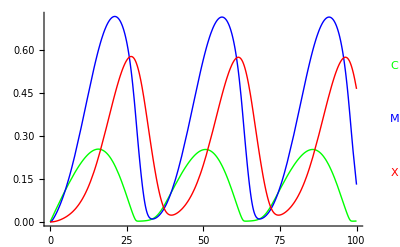

```mathematica
tc=run[circuit,
plot-> True,
initialConditions-> {C-> 0,M-> 0, X-> 0}, 
plotVariables-> {C,M,X},
rates-> rules];
```

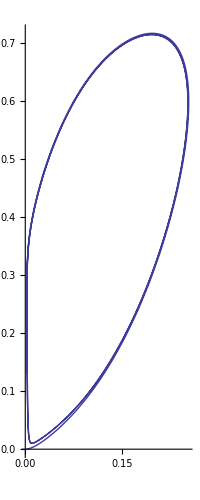

```mathematica
ParametricPlot[{C[t],M[t]}/.tc, {t,0,100}]
```